```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
StarRates={Rstar,Hstar,Fstar}/.{λ->Growth,μ->Mortality,m->Maintenance,α->Resourcegrowth,σ->Starvation,ρ->Recovery};
```

```mathematica
HF=StarRates[[2;;3]];
HFM= HF*Maintenance;
```

Energy equivalence hypothesis

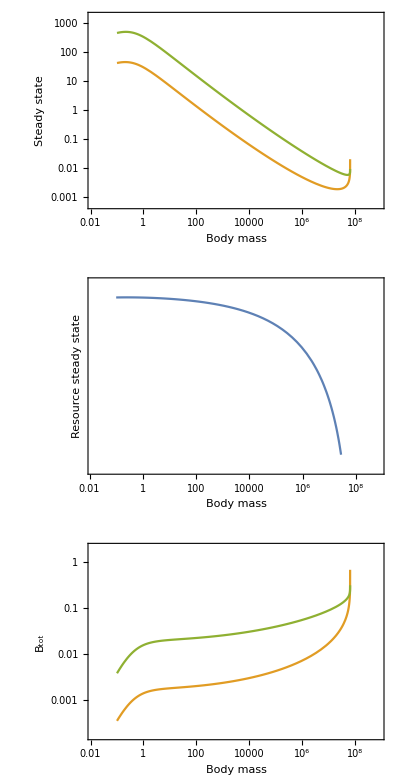

```mathematica
Cplot=GraphicsGrid[{{
LogLogPlot[HF,{M,.1,10^8},Frame->True,FrameLabel->{"Body mass","Steady state"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]},{
LogLogPlot[HFM,{M,.1,10^8},Frame->True,FrameLabel->{"Body mass","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]},{
LogLogPlot[StarRates[[1]],{M,.1,10^8},Frame->True,FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf",Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf

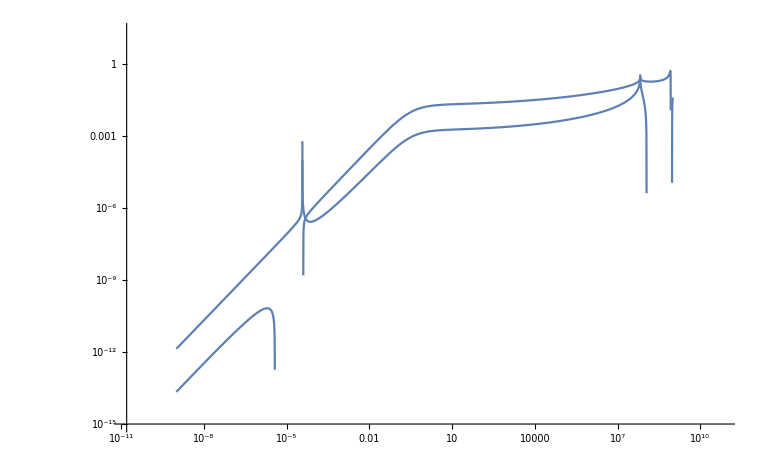

```mathematica
LogLogPlot[Re[HFM],{M,10^-9,10^9}]
```

```mathematica
FindMaximum[Re[HFM[[1]]],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.59227,{M→6.53794×10^7}}

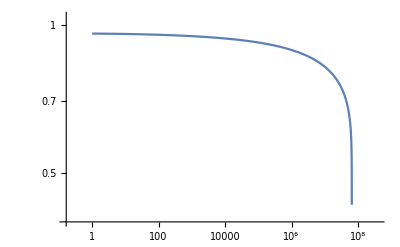

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^9},PlotRange->All]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}